```mathematica
tweetNum = 500
donaldtrump=Import["C:\\Users\\Juan Jose Viafara\\OneDrive\\Escritorio\\I\\UNIVERSIDAD JUAN JOSE\\semestre 7\\Sist. Comp. Mod. Redes\\proyecto\\hashtag_donaldtrump.csv", "Dataset", "HeaderLines"-> 1][1;;tweetNum];

donaldtrump
```

500

Dataset[<>]

```mathematica
(* Función para extraer temas de un tweet *)
getTopics[tweet_] := If[StringQ[tweet],Select[TextWords[tweet], StringMatchQ["#" ~~ ___]],{}];


(* Obtener los temas del dataset *)
allTopics = {}
For[j=1,j<=tweetNum,j++, allTopics = Append[allTopics, getTopics[donaldtrump[j, "tweet"]]]]

allTopics = Select[Tally[Flatten[allTopics]], Last[#] >= 2 &][[All, 1]]
Print[Length[allTopics]]
```

{}

{#JoeBiden,#DonaldTrump,#donaldtrump,#Trump,#Iowa,#TheReidOut,#trump,#WhiteHouse,#Election2020,#AmyConeyBarrett,#KamalaHarris,#SCOTUS,#SupremeCourtConfirmation,#NYPost,#censorship,#China,#Trump2020LandslideVictory,#Trump2020,#MAGA,#KAG,#America,#AmericaFirst,#Winning,#Vote,#VoteInPerson,#Ukraine,#FactCheck,#Biden,#Election,#Politics,#President,#Republican,#TrumpCovid19,#TrumpIsALaughingStock,#TrumpIsALoser,#VoteHimOut,#VoteBlueToEndThisNightmare,#MAGA2020,#USElection2020,#TrumpLiedPeopleDied,#Democrats,#TRUMP,#public,#USA,#COVID19,#SuperSpreader,#TrumpRally,#TrumpRallyDesMoines,#pandemic,#BidenHarris2020,#Debates2020,#biden,#AOC,#Covid19,#TrumpLiesAmericansDie,#herdimmunity,#HunterBiden,#BidenHarris,#TrumpPence2020,#realDonaldTrump,#coronavirus,#BidenHarrisToSaveAmerica,#politics,#USnews,#Obama,#tRump,#BlacksForTrump,#LawAndOrder,#BillBarr,#FourMoreYears,#TheWeek,#HunterBidenEmails,#USElection,#Pence,#Harris,#WCPH2020,#WearAMask,#MaskUp,#COVIDIOTS,#fools,#TrumpFakedCovid,#TrumpFailed,#DumpTrump,#TrumpCrimeFamily,#Debate2020,#FoxNews,#CNN,#Trump2020Landslide,#bidenharris2020,#election,#IceCube,#hunterbiden,#trump2020,#VoteBidenHarris2020,#covid,#TrumpTrain,#NorthCarolina,#lies,#corruption,#VoteBiden,#TrumpIsANationalDisgrace,#maga,#vote,#freedom,#KAG2020,#TRUMP2020,#Giuliani,#Russia,#Corruption,#GOP,#Republicans,#TruthMatters,#kayleighmcenany,#VoteHimOut2020,#MAGA2020Landslide,#Resist,#POTUS,#MSNBC,#facebook,#twitter,#NancyPelosi,#auspol,#Twitter,#Facebook,#USPresidentialElections2020,#ElectionDay,#VoteThemAllOut,#HealthAlert,#GrabYourWallet,#TrumpToll,#BidenTownHall,#BidenHarrisLandslide2020,#BoycottMSNBC,#TrumpSupporters,#People,#TrumpVirus,#TrumpVirusDeathToll215K,#MitchMcConnell,#TrumpKillsUs,#TrumpIsNotWell,#VetsAgainstTrump,#Veteran,#VeteransForTrump,#LindseyMustGo,#MoscowMitch,#MoscowMitchTraitor,#LindseyGraham,#mass,#pathetic,#fakenews,#democracy,#PUTIN,#EnemyOfThePeople,#icecube,#TrumpVirusDeathToll275K,#Americans,#GOPDeathCult,#Covid,#ProsecuteThemAll,#VoteBidenHarris,#VoteBlue,#TrumpProjection,#AmericaOrTrump,#AmericaNeedsPennsylvania,#Dump,#TrumpTaxes,#PromisesMadePromisesKept,#UnitedStates,#usa,#COVID,#TrumpIsACompleteFailure,#regeneron,#TrumpRallyIowa,#Democrat,#DumpTrump2020,#News,#Putin,#voting,#DonaldJTrump,#DrainTheSwamp,#NBC,#WolfBlitzer,#US,#SuperSpreaderTrump,#Entrepreneur,#sidehustle,#CloudComputing,#JavaScript,#MachineLearning,#onlinejobs,#Onlineclass,#startup,#BusinessTravel,#linux,#serverless,#DigitalMarketingTools,#remotelearning,#remotejobs,#MelaniaTrump,#BarronTrump,#FactsMatter,#BidenGate,#TrumpLandslide2020,#FirstAmendment,#VOTE,#TikTok,#TwitterCensorship,#tcot,#wiright,#wipolitics,#UniteBlueNoMatterWho,#UniteBlue,#Murdoch,#TrumpCovid,#BoycottNBC,#TrumpRallyFlorida,#BoycottTrumpTownHall,#trumpbook,#BIDEN,#right}

220

```mathematica
clearTopic[topic_] := ResourceFunction["ToCamelCase"][
													ToLowerCase[
																ResourceFunction["FromCamelCase"][StringDrop[topic, 1]]]]
filterTopics[topics_] := Select[First /@ GatherBy[clearTopic /@ topics, ToLowerCase], LanguageIdentify[#] === Entity["Language", "English"] &];


filteredTopics = filterTopics[allTopics]
Print[Length[filteredTopics]]
```

{joeBiden,donaldTrump,trump,iowa,whiteHouse,election2020,amyConeyBarrett,nypost,censorship,china,trump2020landslideVictory,trump2020,kag,america,americaFirst,winning,vote,ukraine,factCheck,biden,election,politics,president,republican,trumpCovid19,trumpIsAlaughingStock,trumpIsAloser,voteHimOut,voteBlueToEndThisNightmare,uselection2020,trumpLiedPeopleDied,democrats,public,covid19,superSpreader,trumpRally,trumpRallyDesMoines,pandemic,bidenHarris2020,debates2020,trumpLiesAmericansDie,herdimmunity,hunterBiden,bidenHarris,trumpPence2020,usnews,obama,blacksForTrump,lawAndOrder,fourMoreYears,theWeek,hunterBidenEmails,uselection,pence,harris,wcph2020,wearAmask,maskUp,covidiots,fools,trumpFakedCovid,trumpFailed,dumpTrump,trumpCrimeFamily,debate2020,foxNews,cnn,trump2020landslide,covid,trumpTrain,northCarolina,lies,corruption,voteBiden,trumpIsAnationalDisgrace,freedom,kag2020,gop,republicans,truthMatters,kayleighmcenany,voteHimOut2020,resist,facebook,twitter,nancyPelosi,auspol,uspresidentialElections2020,electionDay,voteThemAllOut,healthAlert,grabYourWallet,trumpToll,bidenTownHall,boycottMsnbc,trumpSupporters,people,mitchMcConnell,trumpKillsUs,trumpIsNotWell,vetsAgainstTrump,veteran,lindseyMustGo,moscowMitch,moscowMitchTraitor,lindseyGraham,mass,pathetic,fakenews,democracy,enemyOfThePeople,americans,gopdeathCult,prosecuteThemAll,voteBlue,trumpProjection,americaOrTrump,americaNeedsPennsylvania,dump,trumpTaxes,promisesMadePromisesKept,unitedStates,trumpIsAcompleteFailure,trumpRallyIowa,democrat,dumpTrump2020,news,voting,donaldJtrump,drainTheSwamp,nbc,us,superSpreaderTrump,sidehustle,cloudComputing,machineLearning,onlinejobs,onlineclass,startup,businessTravel,serverless,digitalMarketingTools,remotelearning,remotejobs,factsMatter,trumpLandslide2020,firstAmendment,twitterCensorship,tcot,wiright,wipolitics,uniteBlueNoMatterWho,uniteBlue,murdoch,trumpCovid,boycottNbc,trumpRallyFlorida,boycottTrumpTownHall,trumpbook,right}

160

```mathematica
getActors[tweet_] := If[StringQ[tweet], StringCases[tweet, "@" ~~ WordCharacter..],{}];


(* Obtener las mensiones del dataset *)
allActors = {}
For[j=1,j<=tweetNum,j++, allActors = Append[allActors, getActors[donaldtrump[j, "tweet"]]]]

allActors = Select[Tally[Flatten[allActors]], Last[#] >= 2 &][[All, 1]]
Print[Length[allActors]]
```

{}

{@realDonaldTrump,@nypost,@jack,@JoeBiden,@RealDonaldTrump,@GOP,@cnnbrk,@MarcInPhoenix,@CIAspygirl,@RudyGiuliani,@Twitter,@PressSec,@CNN,@andersoncooper,@icecube,@TheDemocrats,@OMAROSA,@DonaldJTrumpJr,@POTUS,@newsmax,@thehill,@maddow,@WhiteHouse,@TwitterSafety,@charliekirk11,@KamalaHarris,@senatemajldr,@kayleighmcenany,@BarackObama,@donwinslow,@thereidout,@DrDenaGrayson,@womensmarch,@Women4Biden,@MarchForScience,@March4RLivesLA,@MarchForTruth17,@nbc,@MSNBC,@NBCNews,@ABC,@CBSNews,@CNNPolitics,@bpolitics,@business,@ABCPolitics,@MaryBriggs1,@kevinbossuet,@SudRadio,@Acosta,@YouTube,@PaulaReidCBS,@wolfblitzer,@weijia,@CBSPolitics,@NBCPolitics,@KatyTurNBC,@jaketapper,@FiringLineShow,@npratc,@MeidasTouch,@morningmika,@SavannahGuthrie,@funder,@RawStory,@chipfranklin,@ddlovato,@FoxNews,@KlausIohannis,@DevinNunes,@tteribul,@MariaEHerrera1,@lorettaslaught1,@no,@Crixiest,@dottyinaction,@BurkhardConnie,@BIvy0303,@SnowWhiteheart,@AndyAccioli,@aSnarkyActivist,@RobertEdgemon2,@dabbienormal11}

83

```mathematica
getAsso[tweet_]:= Module[{tweetActors=If[StringQ[tweet["user_screen_name"]], Append[getActors[tweet["tweet"]], "@"<>tweet["user_screen_name"]], getActors[tweet["tweet"]]], tweetTopics=ToLowerCase[filterTopics[getTopics[tweet["tweet"]]]], assoc = Association[{}], setVal, setValActors}, 

 setVal[topic_]:= AssociateTo[assoc, "#"<>topic -> If[MemberQ[tweetTopics, ToLowerCase[topic]], 
 2*tweet["retweet_count"] + tweet["likes"]+1 , 0]];
 Map[setVal,filteredTopics];
 setValActors[actor_] :=  AssociateTo[assoc, actor -> If[MemberQ[tweetActors, actor], 
 2*tweet["retweet_count"] + tweet["likes"]+1 , 0]];
 Map[setValActors,allActors];
 assoc
 ]

 assocs= {}
 For[j=1,j<=tweetNum,j++, assocs = Append[assocs, getAsso[donaldtrump[j]]]]
 dataset = Dataset[assocs]
```

{}

Dataset[<>]

```mathematica
transformToMatrix[dataset_]:=Module[{filas={}, columnas={}}, For[i=1, i<=Length[dataset],i++, columnas={};For[j=1, j<=Length[dataset[i]],j++, columnas= Append[columnas, dataset[i][j]]];filas= Append[filas, columnas]]; 
filas
]
wholeMatrix={}
wholeDataset = Module[{matrix= transformToMatrix[dataset], assocs = Association[{}], keys = dataset[Keys][[1]], assoc},
	wholeMatrix = Transpose[matrix] . matrix;
	Do[
		assoc = Association[{}];
		Do[
			AssociateTo[assoc, keys[[j]] -> If[i!=j, wholeMatrix[[i,j]], 0]]
			,{j, Length[keys]}
			];
		AssociateTo[assocs, keys[i]-> assoc];
		, {i, Length[keys]}
		];
	Dataset[assocs]
]
```

{}

Dataset[<>]

{}

{}

{}

«1 more identical outputs»

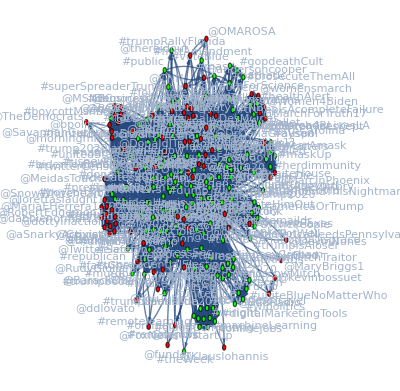

```mathematica
edges={}
edgesColor={}
vertex={}
edgesWeight={}
buildEdge[row_, rowName_] := For[
	i=1, i<=Length[row], i++,
	If[row[i]!=0, edges=Append[edges, rowName -> Keys[row][i] ]; edgesWeight=Append[edgesWeight, rowName -> Keys[row][i]-> row[i]]]
]

Do[
	buildEdge[wholeDataset[j], Keys[wholeDataset][j]]; 
	vertex = Append[vertex, 
		If[StringStartsQ[Keys[wholeDataset][j], "#"],
		 Style[Keys[wholeDataset][j], Green], Style[Keys[wholeDataset][j], Red]]], 
	{j, Length[wholeDataset]}];
  


graph = Graph[vertex,edges, VertexLabels -> "Name", GraphLayout->"SpringElectricalEmbedding", EdgeWeight->edgesWeight]
```

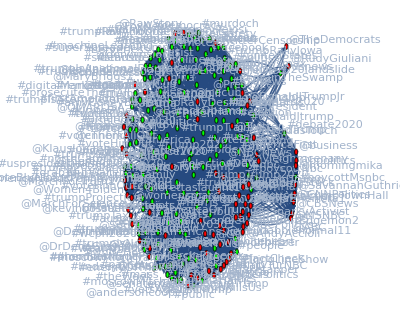

-Graphics-

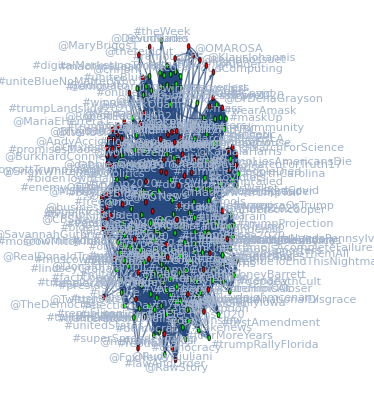

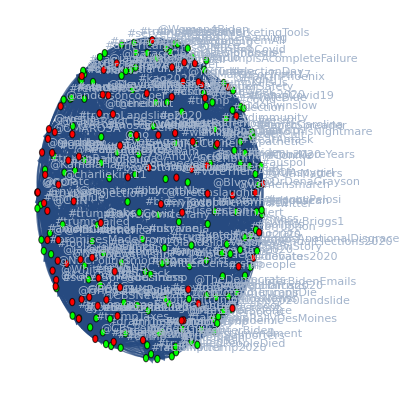

```mathematica
Do[Print[Graph[vertex,edges, VertexLabels -> "Name", EdgeWeight->edgesWeight, GraphLayout->l]], {l,{"SpringEmbedding", "SpringElectricalEmbedding", "GravityEmbedding",  "SphericalEmbedding"}}]
```

```mathematica
centralities = DegreeCentrality[graph];

HighlightGraph[graph, VertexList[graph] ,VertexSize -> Thread[VertexList[graph] -> Rescale[centralities]]]
```

-Graphics-

```mathematica
-Graphics--Graphics-
```

-Graphics--Graphics-

```mathematica
FindGraphCommunities[graph];
CommunityGraphPlot[graph, %]
```

-Graphics-

```mathematica
BetweennessCentrality[graph];
HighlightGraph[graph, VertexList[graph], 
 VertexSize -> Thread[VertexList[graph] -> Rescale[%]]]
```

-Graphics-

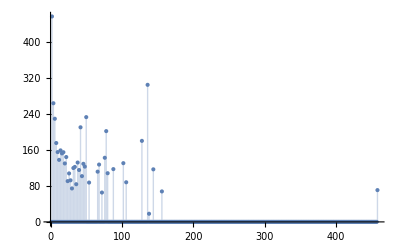

```mathematica
ListPlot[Rest[MeanDegreeConnectivity[graph]], Filling -> Axis]
```

```mathematica
MeanNeighborDegree[graph];
HighlightGraph[graph, VertexList[graph], 
 VertexSize -> Thread[VertexList[graph] -> Rescale[%]]]
```

-Graphics-